## z0 1.2

```mathematica
Subscript[zDe, 1]=1.2;
```

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1.2;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.05,0.6,(0.6-0.05)/30}];
gtil=Table[γ,{γ,0.0001,0.06,(0.06-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
```

```mathematica
tfF=Table[Table[AllTrue[conditions1[[q,p]],#==True&],{p,1,nE2}],{q,1,nE3}];
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

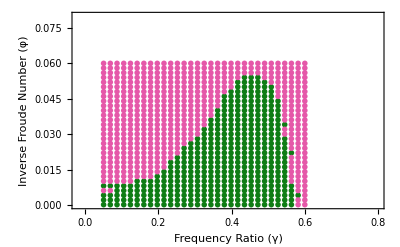

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]
,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1.2;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]]===True,{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

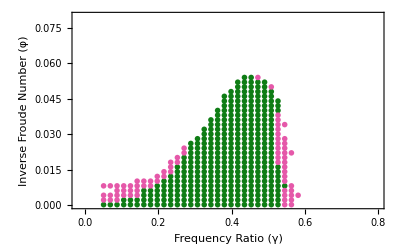

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=35;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1.2;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[p]][[;;2]]==={True,True},{p,1,nE2}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

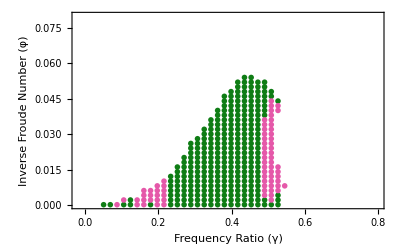

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]],Style[falsepoints4,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=250;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=1.2;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i]]=={True,True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

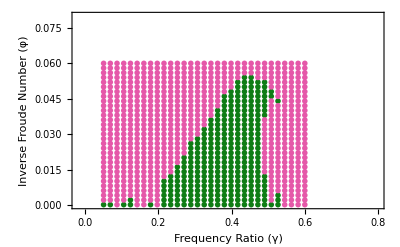

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofz012TPU.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofz012FPU.mx",finalfalsepoints];
```

## z0 0.6

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=5;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=0.6;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

mtil=Table[ϕ,{ϕ,0.025,0.6,(0.6-0.025)/30}];
gtil=Table[γ,{γ,0.0001,0.06,(0.06-0.0001)/30}];
nE2=Length[mtil];
nE3=Length[gtil];
```

```mathematica
Quiet[Table[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->mtil[[p]],γ->gtil[[q]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p,q]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[yPDe, nE+1]]-Abs[Subscript[yPDe, nE]])]<10^-6,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-6}


},{p,1,nE2}],{q,1,nE3}]];
```

```mathematica
mg=Table[Table[{mtil[[i]],gtil[[j]]},{i,1,nE2}],{j,1,nE3}];
conditions=Table[Table[Subscript[condi, p,q],{p,1,nE2}],{q,1,nE3}];
conditions1=Table[If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions[[q]],{q,1,nE3}];
fistCon=Table[Table[First[conditions1[[q,p]]],{p,1,nE2}],{q,1,nE3}];
truepoints=Table[Pick[mg[[q]],fistCon[[q]],True],{q,1,nE3}];
falsepoints=Flatten[Table[Pick[mg[[q]],fistCon[[q]],False],{q,1,nE3}],1];
```

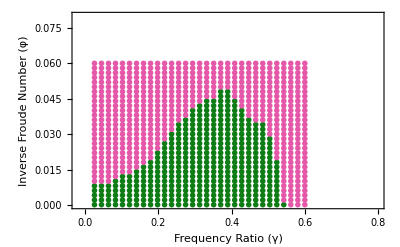

```mathematica
Show[ListPlot[{Style[Flatten[truepoints,1],ColorData["AvocadoColors",0.3]],Style[falsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Second Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=20;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=0.6;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=Flatten[truepoints,1];
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions2=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
firstCon2=Table[First[conditions2[[p]]],{p,1,nE2}];
truepoints2=Pick[Flatten[truepoints,1],firstCon2,True];
falsepoints2=Pick[Flatten[truepoints,1],firstCon2,False];
```

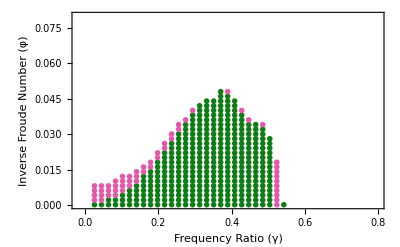

```mathematica
Show[ListPlot[{Style[truepoints2,ColorData["AvocadoColors",0.3]],Style[falsepoints2,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Third Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=50;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=0.6;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=truepoints2;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions3=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon3=Table[conditions3[[i,;;2]]=={True,True},{i,1,Length[conditions3]}];
truepoints4=Pick[truepoints2,secondCon3,True];
falsepoints4=Pick[truepoints2,secondCon3,False];
```

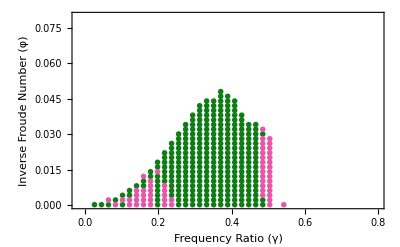

```mathematica
Show[ListPlot[{Style[truepoints4,ColorData["AvocadoColors",0.3]],Style[falsepoints4,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

### Fourth Filter

```mathematica
Clear[sol,fulsoly,fulsolz,dsoly,dsolz,ddsoly,ddsolz,yf,tDe,yDe,yPDe,vDe,sgnvDe,p0De,parameters,intime,trfa,times,tgrps,fk,fb,ltri,α,b,g,zDe,zPDe,k,leq,tftimes,timesint,times,m,mg,dLspeed,ke,percentCong,stepfreq,steplength,meanz,meanZ,amp,energy,mtil,gtil,condi,stop];

nE=350;

Subscript[zf, 1]=0;
Subscript[yf, 1]=0;
Subscript[yDe, 1]=-0.05;
Subscript[zDe, 1]=0.6;

Subscript[yPDe, 1]=0.015;
Subscript[zPDe, 1]=0;

Subscript[tDe, 1]=0;
period=(4Pi);

ϕγ=falsepoints4;
nE2=Length[ϕγ];
```

```mathematica
Quiet[Table[{Table[{solutions={},
seeds=Table[i,{i,Subscript[tDe, k]+0.2,Subscript[tDe, k]+ period,0.25}],
parameters=Table[{ldev->1.5*1,l0->1,b->0,ϕ->ϕγ[[p,1]],γ->ϕγ[[p,2]]},{p,1,nE2}],
Subscript[leq, k][t]=l0-ldev Cos[(t-Subscript[tDe, k])],
Subscript[ltri, k][t]=Sqrt[(y[t]-Subscript[yf, k])^2+(z[t]-Subscript[zf, k])^2],
Subscript[fk, k][t]=(Subscript[leq, k][t]-Subscript[ltri, k][t]),
Subscript[fb, k][t]=0(D[Subscript[leq, k][t],t]-D[Subscript[ltri, k][t],t]),
Subscript[sol, k]=NDSolve[Evaluate[{ y''[t]==ϕ^2(Subscript[fk, k][t]+Subscript[fb, k][t])(y[t]-Subscript[yf, k])/(Subscript[ltri, k][t]),
z''[t]==ϕ^2((Subscript[fk, k][t]+Subscript[fb, k][t])(z[t]-Subscript[zf, k])/(Subscript[ltri, k][t]))-γ
,y[Subscript[tDe, k]]==Subscript[yDe, k],y'[Subscript[tDe, k]]==Subscript[yPDe, k],z[Subscript[tDe, k]]==Subscript[zDe, k],z'[Subscript[tDe, k]]==Subscript[zPDe, k]}/.parameters[[p]]],{y[t],z[t]},{t,Subscript[tDe, k],Subscript[tDe, k]+period}],

Subscript[fulsoly, k]=(y[t]/. Subscript[sol, k])[[1]],
Subscript[fulsolz, k]=(z[t]/. Subscript[sol, k])[[1]],
Subscript[dsoly, k]=D[Subscript[fulsoly, k],t],
Subscript[dsolz, k]=D[Subscript[fulsolz, k],t],

Do[
sol2=Quiet@FindRoot[Subscript[dsoly, k]==Subscript[yPDe, k],{t,seed}];
If[Not[Head[sol2]===FindRoot],AppendTo[solutions,sol2]],{seed,seeds}
],

times=Select[t/.solutions,(Subscript[tDe, k]+0.2)<#<(Subscript[tDe, k]+period)&],
ys=Flatten[(Subscript[dsoly, k]/.t->times)],
tf=Table[(ys[[i]]-Subscript[yPDe, k])<10^-6,{i,1,Length[ys]}],


Subscript[tDe, k+1]=Min[DeleteDuplicates[Pick[times,tf]]],



Subscript[yDe, k+1]=(Subscript[fulsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zDe, k+1]=(Subscript[fulsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[yPDe, k+1]=(Subscript[dsoly, k]/.t->Subscript[tDe, k+1]),
Subscript[zPDe, k+1]=(Subscript[dsolz, k]/.t->Subscript[tDe, k+1]),

Subscript[zf, k+1]=0,
Subscript[yf, k+1]=Subscript[yDe, k+1]+Abs[Subscript[yDe, 1]]

}


,{k,1,nE}],
zt=Piecewise[Table[{Flatten[z[t]/. Subscript[sol, i]],Subscript[tDe, i]<=t<=Subscript[tDe, i+1]},{i,1,nE}]],
Subscript[condi, p]={AllTrue[Flatten[Table[zt/.t->t,{t,0,Subscript[tDe, nE],0.2}]],#>=0&],
Abs[(Abs[Subscript[zPDe, nE+1]]-Abs[Subscript[zPDe, nE]])]<10^-2,
Abs[(Abs[Subscript[zDe, nE+1]]-Abs[Subscript[zDe, nE]])]<10^-2}


},{p,1,nE2}]];
```

```mathematica
conditions=Table[Subscript[condi, p],{p,1,nE2}];
conditions4=If[AllTrue[#,BooleanQ],#,ConstantArray[False,Length[#]]]&/@conditions;
secondCon4=Table[conditions4[[i,;;2]]=={True,True},{i,1,Length[conditions4]}];
truepoints5=Pick[falsepoints4,secondCon4,True];
falsepoints5=Pick[falsepoints4,secondCon4,False];
```

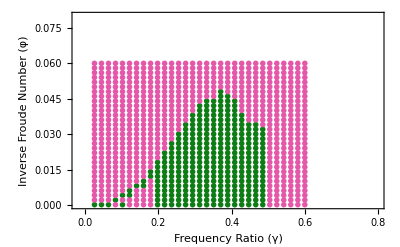

```mathematica
finaltruepoints=Union[truepoints5,truepoints4];
finalfalsepoints=Union[falsepoints5,falsepoints2,falsepoints];
Show[ListPlot[{Style[finaltruepoints,ColorData["AvocadoColors",0.3]],Style[finalfalsepoints,ColorData["FruitPunchColors",0.9]]},PlotStyle->{PointSize[0.01]}]

,LabelStyle->{Black,17},FrameLabel->{{"Inverse Froude Number (φ)",None},{"Frequency Ratio (γ)",None}},PlotRange->{{-0.02,0.8},{0,0.08}},Frame->True]
```

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofz006TPU.mx",finaltruepoints];
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofz006FPU.mx",finalfalsepoints];
```